# Exercise 15

As with all of the exercises you will complete in this course, you will be expected to turn your *.nb file in to the course TA before the next lecture.  Please do so by e-mailing your completed exercise file to Lan Yu (ece329.uiuc@gmail.com), make sure you name the file using the following notation: “Exn_Last_First.nb”, where n is the Exercise number (in this case, 15), and First and Last would be your first and last name.  So my submission to Lan for this exercise would be titled “Ex15_Wasserman_Dan.nb”.  You will receive full credit for your exercise if it turned in before the next lecture (Lecture n+1).  No late submissions will be accepted.

## Objective/Overview:

In today’s Lecture (15) we discussed the concent of self-inductance.  We talked about how the current in a current-carrying loop-type structure is related to the magnetic flux through that loop via the structure’s Inductance (L): Ψ=LI.  In particular, we looked at three examples: the solenoid, the coax cable, and the parallel plate capacitor.  The coax and parallel plate capacitor will become hugely important when we discuss transmission lines.  Today we are going to go back to the solenoid we modeled in Exercise 13 and look at its Inductance.

```mathematica
ClearAll[bloopxz]
```

## Calculating the Inductance of a Solenoid

In our previous exercise, we were able to calculate the inductance of a Solenoid, basically modeled from scratch!  Let’s go back to that as our starting point.  We will cut and paste the expression for B field from a single current loop below, assuming  (μ_o I)/(4π)=1:

```mathematica
bloopxz={(π zo (1+xo^2+zo^2-√((-1+xo^2)^2+2 (1+xo^2) zo^2+zo^4)))/(xo √(xo^4+2 xo^2 (-1+zo^2)+(1+zo^2)^2)),-(π (-1+xo^2+zo^2-√((-1+xo^2)^2+2 (1+xo^2) zo^2+zo^4)))/(√(xo^4+2 xo^2 (-1+zo^2)+(1+zo^2)^2))}
```

{(π zo (1+xo^2+zo^2-√((-1+xo^2)^2+2 (1+xo^2) zo^2+zo^4)))/(xo √(xo^4+2 xo^2 (-1+zo^2)+(1+zo^2)^2)),-(π (-1+xo^2+zo^2-√((-1+xo^2)^2+2 (1+xo^2) zo^2+zo^4)))/(√(xo^4+2 xo^2 (-1+zo^2)+(1+zo^2)^2))}

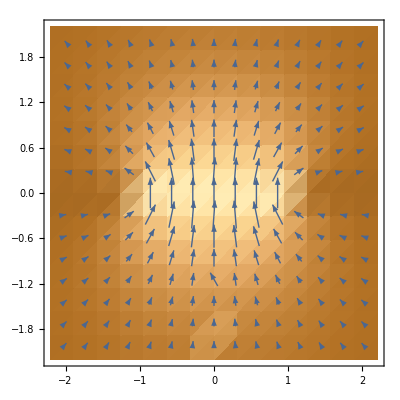

```mathematica
VectorDensityPlot[bloopxz,{xo,-2,2},{zo,-2,2}]
```

To turn this into a solenoid, we need to add a bunch of loops together and calculate the field from these.  We will ignore the field in x, and assume that all of our field is in the z-direction.

```mathematica
bloop1z[xo_,zo_]:=-(π (-1+xo^2+zo^2-√((-1+xo^2)^2+2 (1+xo^2) zo^2+zo^4)))/(√(xo^4+2 xo^2 (-1+zo^2)+(1+zo^2)^2))
```

```mathematica
bloopNz[xo_,zo_,N_]:=Sum[bloop1z[xo,zo-(-2+i/N)],{i,0,4*N}]
```

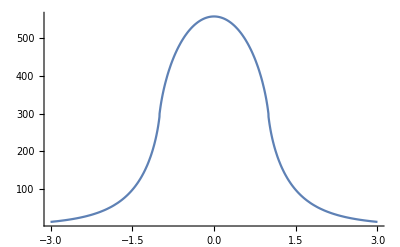

```mathematica
Plot[bloopNz[xo,0,40],{xo,-3,3}, PlotRange->Full]
```

This gives us the B field vs xo at zo=0.  We can use rotational symmetry, and add in our (μ_o I)/(4π) term to find the flux...we just have to remember that to integrate in cylindrical coordinates, we use 2πrdr or in our case 2πxodxo, and integrate from xo=0 to xo=1 (the radius of our solenoid).  Our inductance is just nΨ/I, so we can simplify to find Inductance

```mathematica
muo=1.2567*10^-6;
```

The inductance for the solenoid above, which has n=N*4, will be

```mathematica
solind=4*40*(muo/(4*Pi))*NIntegrate[2*Pi*xo*bloopNz[xo,0,40],{xo,0,1}]
```

0.0226806

Use the analytical expression we derived in class to determine the inductance of our solenoid, and compare this to your numerical result

```mathematica
indderived=40^2*muo*Pi*4
```

0.0252675

Cool!  Pretty close!

### Solenoid as a Lumped Circuit Element

We were able to calculate the inductance of our solenoid above, so now we should be able to put the solenoid in a circuit and look at the behavior of the circuit vs time.  Remember, the “voltage” or EMF we generate across our inductor is directly linked to the inductance by ℰ=-LⅆI/ⅆt.  Let’s consider the following circuit, as shown below:
-Graphics-
Here we have an inductor in series with a resistor R, and a battery with voltage V.  We know that the total voltage around the loop is zero, so we can write:
V(t)-I(t)R-LⅆI/ⅆt=0
We should be able to introduce a V(t) and solve for the response of the circuit, giving the EMF across the inductor, as well as the energy stored in the inductor.  Let’s try this for V(t)=HeavisideTheta(t), assuming R=50Ω

```mathematica
vt=Piecewise[{{0,t<0},{1,t≥ 0}}]
```

Piecewise[{{0, t<0}, {1, t≥0}, {0, True}}]

```mathematica
sol=DSolve[vt-50*it[t]-solind*it'[t]==0,it[t],t]
```

{{it[t]→ⅇ^(-2204.53 t) C[1]+ⅇ^(-2204.53 t) (Piecewise[{{0., t≤0.}, {-0.02+0.02 ⅇ^(2204.53 t), True}}])}}

We know that as t->∞, dI/dt->0, the system reaches steady state.  This means that all of the voltage must be dropped over the resistor, so I=0.02A. The equation gets this right, regardless of C[1].  At t=0, we expect i(t)=0. That means that C[1]=0.

```mathematica
itsol=ⅇ^(-2204.5277693381267 t) (Piecewise[{{0., t≤0.}, {-0.02+0.02 ⅇ^(2204.5277693381267 t), True}}])
```

ⅇ^(-2204.53 t) (Piecewise[{{0., t≤0.}, {-0.02+0.02 ⅇ^(2204.53 t), True}}])

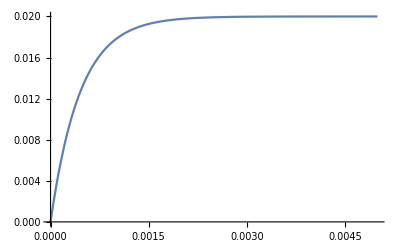

```mathematica
Plot[itsol,{t,0,.005}, PlotRange->Full]
```

The EMF across the Inductor is EMF=-LⅆI/ⅆt

```mathematica
dIdt=D[itsol,t]
```

-2204.53 ⅇ^(-2204.53 t) (Piecewise[{{0., t≤0.}, {-0.02+0.02 ⅇ^(2204.53 t), True}}])+ⅇ^(-2204.53 t) (Piecewise[{{0, t<0}, {44.0906 ⅇ^(2204.53 t), t>0}, {Indeterminate, True}}])

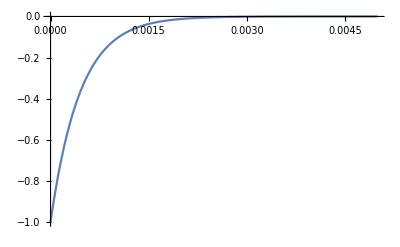

```mathematica
Plot[-solind*dIdt,{t,0,.005}, PlotRange->Full]
```

The energy stored in the Inductor is 0.5*L*I^2

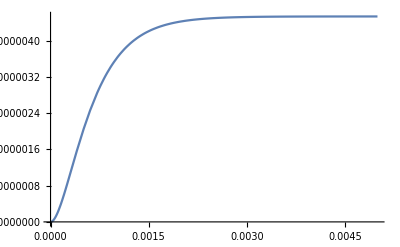

```mathematica
Plot[0.5*solind*itsol^2,{t,0,.005}, PlotRange->Full]
```

### Inductor in a circuit with a time-varying voltage

Let’s now consider a V(t)=Cos[1000*t].  Solve for the response of the circuit and plot V(t), EMF, and the energy stored inteh inductor as functions of time:

```mathematica
vt1=Cos[1000*t]
```

Cos[1000 t]

```mathematica
sol1=DSolve[vt1-50*it1[t]-solind*it1'[t]==0,it1[t],t]
```

{{it1[t]→ⅇ^(-2204.53 t) C[1]+44.0906 ((0.000376203+2.71051×10^-20 ⅈ) Cos[1000. t]+0.00017065 Sin[1000. t])}}

```mathematica
itsol1=44.09055538676253 ((0.0003762029575283437+2.710505431213761*^-20 ⅈ) Cos[1000. t]+0.00017065013322163433 Sin[1000. t])
```

44.0906 ((0.000376203+2.71051×10^-20 ⅈ) Cos[1000. t]+0.00017065 Sin[1000. t])

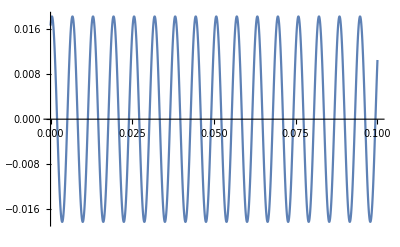

```mathematica
Plot[itsol1,{t,0,.1}, PlotRange->Full]
```